```mathematica
Clear[ShowForNodesFull];ShowForNodesFull[nodes_,operation_:First]:=Block[
{
part1=operation[QuadrilateralsWithPattern[nodes,1]],
part2=operation[QuadrilateralsWithPattern[nodes,2]],
part3=operation[QuadrilateralsWithPattern[nodes,3]],
part4=operation[QuadrilateralsWithPattern[nodes,4]],
part5=operation[QuadrilateralsWithPattern[nodes,5]]
},
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]]
},
{Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]], SymbolLevel[#]==4&],{part1,part2,part3,part4,part5}}
]
]
```

```mathematica
ShowGraphs[list_,frameStyle_]:=Map[
Block[{sym=SymbolToSets[#]},
Labeled[Framed[GraphFromSymbol[#],FrameStyle->frameStyle[SymbolToSets[#]]],SetsToLabel2[sym]]
]&,
list
]
```

```mathematica
ShowSols[nodes_,op_:First]:=Table[
Block[
{
start = Select[sol[[1]],MemberQ[sol[[2]],SymbolToSets[#]]&],
other = Select[sol[[1]],!MemberQ[sol[[2]],SymbolToSets[#]]&]
},
ShowGraphs[start,Directive[Dotted,Thick,Orange]&]->
ShowGraphs[other,If[HasQuadrilateralPattern[#],Red,Darker[Green]]&]
],{sol,{ShowForNodesFull[nodes,op]}}]
```

## The first

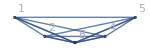
{{-Graphics-16♁35,-Graphics-16♁25,-Graphics-16♁24,-Graphics-14♁26,-Graphics-13♁26}→{-Graphics-26♁35,-Graphics-24♁35,-Graphics-14♁35,-Graphics-14♁25,-Graphics-13♁25,-Graphics-13♁24}}

```mathematica
ShowSols[6,First]
```

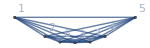
{{-Graphics-16♁27♁35,-Graphics-16♁25♁37,-Graphics-16♁24♁37,-Graphics-14♁26♁37,-Graphics-13♁26♁47}→{-Graphics-26♁35♁47,-Graphics-247♁35,-Graphics-16♁35♁47,-Graphics-16♁25♁47,-Graphics-16♁247,-Graphics-16♁24♁35,-Graphics-14♁27♁35,-Graphics-14♁26♁35,-Graphics-14♁25♁37,-Graphics-13♁25♁47,-Graphics-13♁247}}

```mathematica
ShowSols[7,First]
```

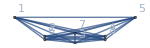
{{-Graphics-16♁27♁35♁48,-Graphics-16♁25♁37♁48,-Graphics-16♁24♁37♁58,-Graphics-14♁26♁37♁58,-Graphics-13♁26♁47♁58}→{-Graphics-16♁247♁58,-Graphics-16♁247♁35,-Graphics-13♁247♁58}}

```mathematica
ShowSols[8,First]
```

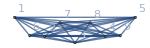
{{-Graphics-16♁27♁359♁48,-Graphics-16♁259♁37♁48,-Graphics-16♁248♁37♁59,-Graphics-148♁26♁37♁59,-Graphics-137♁26♁48♁59}→{-Graphics-17♁26♁359♁48,-Graphics-17♁248♁359,-Graphics-16♁248♁359,-Graphics-148♁27♁359,-Graphics-148♁26♁359,-Graphics-148♁259♁37,-Graphics-137♁259♁48,-Graphics-137♁248♁59}}

```mathematica
ShowSols[9,First]
```

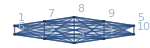
{{-Graphics-1610♁27♁359♁48,-Graphics-1610♁259♁37♁48,-Graphics-1610♁248♁37♁59,-Graphics-148♁2610♁37♁59,-Graphics-137♁2610♁48♁59}→{-Graphics-17♁2610♁359♁48,-Graphics-17♁248♁359♁610,-Graphics-1610♁248♁359,-Graphics-148♁27♁359♁610,-Graphics-148♁2610♁359,-Graphics-148♁259♁37♁610,-Graphics-137♁259♁48♁610,-Graphics-137♁248♁59♁610}}

```mathematica
ShowSols[10,First]
```

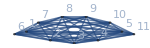
{{-Graphics-1610♁2711♁359♁48,-Graphics-1610♁259♁3711♁48,-Graphics-1610♁248♁3711♁59,-Graphics-148♁2610♁3711♁59,-Graphics-138♁2610♁4711♁59}→{-Graphics-18♁2610♁359♁4711,-Graphics-18♁24711♁359♁610,-Graphics-1610♁28♁359♁4711,-Graphics-1610♁259♁38♁4711,-Graphics-1610♁24711♁38♁59,-Graphics-1610♁24711♁359,-Graphics-1610♁248♁359♁711,-Graphics-148♁2711♁359♁610,-Graphics-148♁2610♁359♁711,-Graphics-148♁259♁3711♁610,-Graphics-138♁259♁4711♁610,-Graphics-138♁24711♁59♁610}}

```mathematica
ShowSols[11,First]
```

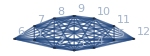
{{-Graphics-1610♁2711♁359♁4812,-Graphics-1610♁259♁3711♁4812,-Graphics-1610♁249♁3711♁5812,-Graphics-149♁2610♁3711♁5812,-Graphics-139♁2610♁4711♁5812}→{-Graphics-1610♁24711♁39♁5812,-Graphics-1610♁24711♁359♁812,-Graphics-139♁24711♁5812♁610}}

```mathematica
ShowSols[12,First]
```

```mathematica
ShowSols[13,First]
```

$Aborted

```mathematica
ShowSols[14,First]
```

$Aborted

## The last

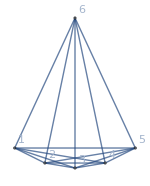
{{-Graphics-356,-Graphics-256,-Graphics-246,-Graphics-146,-Graphics-136}→{-Graphics-35♁46,-Graphics-26♁35,-Graphics-25♁46,-Graphics-25♁36,-Graphics-24♁56,-Graphics-24♁36,-Graphics-24♁35,-Graphics-16♁35,-Graphics-16♁25,-Graphics-16♁24,-Graphics-14♁56,-Graphics-14♁36,-Graphics-14♁35,-Graphics-14♁26,-Graphics-14♁25,-Graphics-13♁56,-Graphics-13♁46,-Graphics-13♁26,-Graphics-13♁25,-Graphics-13♁24}}

```mathematica
ShowSols[6,Last]
```